# Analysis of Packing V3E06L1N02T1_1

Three Vertices, Six Edges, 1 Loop, Combinatorial Number 02, Face Pattern 1, Type 1

```mathematica
-Graphics-;
```

We use the exact same coordinate system for this packing as we use for V3E6L0N2T1_1.  There is a self tangency, so we should be expecting that we will only have one free variable.  We can use the coordinates for the centers of V3E6L0N2T1_1.  Now, the only place where the second parameter appears for V3E6L0N2T1_1 is in the lattice vectors.  However, because of the self tangency, one of the vectors must have a length one; we choose w2 in this case:

```mathematica
Simplify[Sqrt[(((2 /√2 )*Cos[β] )*Cos[α+β])^2+(((2 /√2 )*Cos[β] )*Sin[α+β])^2]==1]
```

√(1+Cos[2 β])==1

```mathematica
Solve[√(1+Cos[2 β])==1,β]
```

{{β→ConditionalExpression[1/2 (-π/2+2 π C[1]),C[1]∈ℤ]},{β→ConditionalExpression[1/2 (π/2+2 π C[1]),C[1]∈ℤ]}}

```mathematica
N[Solve[√(1+Cos[2 β])==1,β]]
```

{{β→ConditionalExpression[0.5 (-1.5708+6.28319 C[1]),C[1]∈ℤ]},{β→ConditionalExpression[0.5 (1.5708+6.28319 C[1]),C[1]∈ℤ]}}

{β→1/2 (π/2)} or {β→π/4)}

So, we substitute in for β.  This makes sense, because with such a self tangency we have an isosceles triangle with side lengths 1, (1/Sqrt[2]), (1/Sqrt[2]).

Notice that the length of the vector along the diagonal from vector 1 to vector 2 must be larger than 1 (the diameter of the big circle) otherwise the two big circles overlap

```mathematica
blah:=Simplify[latticeVectors[[1]]-latticeVectors[[2]]]
```

```mathematica
αβRelation := Simplify[blah[[1]]^2+blah[[2]]^2]
αβRelation
```

2 Sin[α+β]^2

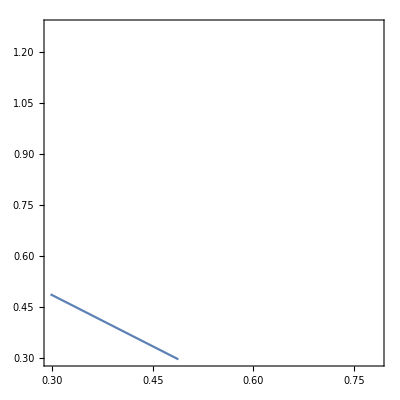

```mathematica
ContourPlot[αβRelation==1,{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])}]
```

## Circle Centers and Radii

```mathematica
centers = {{0,0},{(1/Sqrt[2])*Cos[α],(1/Sqrt[2])*Sin[α]},{(1/Sqrt[2])*Cos[-α]+((2/Sqrt[2])(Cos[π/4]))*Cos[π/4+α],(1/Sqrt[2])*Sin[-α]+((2/Sqrt[2])(Cos[π/4]))*Sin[π/4+α]}}
```

{{0,0},{Cos[α]/(√2),Sin[α]/(√2)},{Cos[α]/(√2)+Cos[π/4+α],-Sin[α]/(√2)+Sin[π/4+α]}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = {
 {(2/Sqrt[2])*Cos[α],0},
{ ((2 /√2 )*Cos[π/4] )*Cos[α+π/4],((2 /√2 )*Cos[π/4] )*Sin[α+π/4]}};
```

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{1,1,0,1},{2,1,0,1},{2,1,1,0},{3,1,0,1},{3,1,1,1},{3,1,1,0}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,
P1:= centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]];
P2:= centers[[edges[[i,1]] ]];
Print["Edge ",i,": Length is ",
Sqrt[FullSimplify[(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2,{0≤α≤ Pi/2,0≤β≤ Pi/2}]]];
]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is 1

Edge 3: Length is 1/(√2)

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Edge 6: Length is 1/(√2)

Edge 7: Length is 1/(√2)

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

To avoid duplication, we take half of the normal range: the normal range that gives duplication is ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4

```mathematica
Simplify[((1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4)-ArcSin[1-1/(√2)])/2]
```

1/8 (π-4 (ArcSin[1-1/(√2)]+ArcTan[(-1+√2)/(√(-1+2 √2))]))

Minus the original upper bound...

```mathematica
FullSimplify[(1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4)-(1/8 (π-4 (ArcSin[1-1/(√2)]+ArcTan[(-1+√2)/(√(-1+2 √2))])))]
```

π/8

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[1]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[1]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,.4,"α"},π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,.3,"α"},ArcSin[1-1/(√2)],π/8}]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_3→ω_1 Tan[2 α],ω_4→Sec[2 α] ω_1,ω_5→Csc[2 α] ω_7,ω_6→1/2 Cos[2 α] Csc[α] Sec[α] ω_7}

Notice that stress ω_1, ω_7 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{α-> 5Pi/6}]]
```

{{0.,0.},{0.,0.},{0.,0.}}

For every α and β in the feasible region (for all Pi/2+ArcCos[2 (-1+√2)]/2< α <  Pi and  Pi/2+ArcCos[2 (-1+√2)]/2<  β < Pi and α >β)  we need to make sure that all ω_i are positive for some choice of ω_1. Try ω_1=1

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.{Subscript[ω, 1]->.1,Subscript[ω, 7]->.1}]]
```

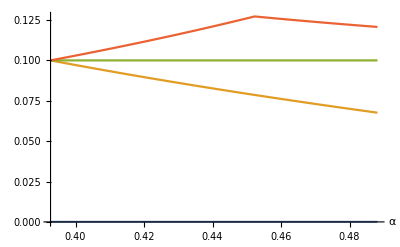

```mathematica
Plot[guts,{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},RegionFunction->Function[{α,β},α>β],AxesLabel->Automatic]
```

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α},Reals],π/8<α<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

π/4+α

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[1]]]/EuclideanDistance[{0,0},latticeVectors[[2]]],{Element[{α},Reals],π/8<α<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

√2 Cos[α]

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

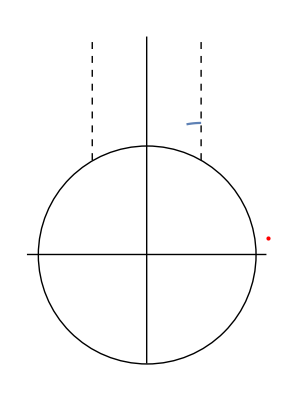

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}],
(*Least dense globally maximally dense point*)
Graphics[{Red,Point[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]}/.{α->2.4907302,β->2.4907302}]}
]]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α},Reals],π/8<α<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

-((-7+4 √2) π Sec[α])/(4 (Cos[α]+Sin[α]))

Plot the density over the parameter space

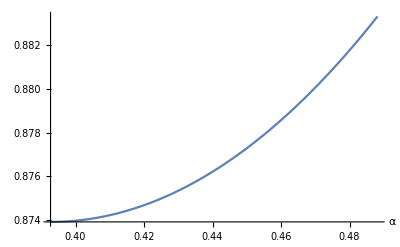

```mathematica
Plot[torusDensity,{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},AxesLabel->Automatic]
```

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

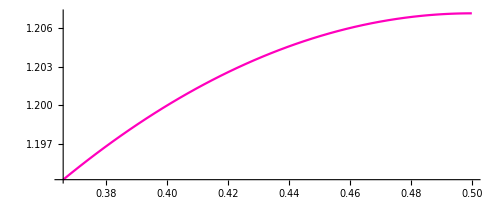

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

Now find the minimum  and maximum density with in the region.

```mathematica
NMinimize[{torusDensity,π/8< α && α < 1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.8739112579475650701175200707375437109016,{α→0.3926990816987241548078304229099378605246}}

```mathematica
NMaximize[{torusDensity,π/8< α && α < 1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.88331053808648840173050934060636024001,{α→0.4881468020762415036628378026915331457068}}